```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metaStructure2={Number,Number,Number,Number,Number,Number,Number,Word,Real};
metaStructure3={Real,Real,Real,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desc3.dat"],metaStructure2];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
ts={35,50,65,80,95,110,125,140,155,170,180,200,215,220,230,240,245,260,275,280,290,300,305,320,335,340,350,360,365,380};
tssz=Dimensions[ts][[1]];
tsadd=PlusMinus[11.3,0.397];
(*Print["Executing: ts = ",ts[[i]]," , i = ",i];*)
tfal=ReadList[StringJoin[descDir,seperator,"tf-Al.dat"],metaStructure3];
tfcu=ReadList[StringJoin[descDir,seperator,"tf-Cu.dat"],metaStructure3];
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l-N[Log10[2]],u+N[Log10[2]],int}]],3];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

```mathematica
pttfmual=Table[{{tfal[[k]][[1]],2tsadd[[2]]},{tfal[[k]][[2]],tfal[[k]][[4]]}},{k,1,tssz}];
pttfmucu=Table[{{tfcu[[k]][[1]],2tsadd[[2]]},{tfcu[[k]][[2]],tfcu[[k]][[4]]}},{k,1,tssz}];
pttf2mual=Table[{{tfal[[k]][[1]],2tsadd[[2]]},{tfal[[k]][[5]],tfal[[k]][[7]]}},{k,1,tssz}];
pttf2mucu=Table[{{tfcu[[k]][[1]],2tsadd[[2]]},{tfcu[[k]][[5]],tfcu[[k]][[7]]}},{k,1,tssz}];
EDAListPlot[pttfmual,pttfmucu,Joined->True,Frame->True,FrameLabel->{"t_s(s)","⟨OverBar[t_f]⟩ ± σ(s)"},PlotRange->{{35,420},{0.04,0.09}},PlotLegends->{"Al","Cu"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Medium}]
EDAListPlot[pttf2mual,pttf2mucu,Joined->True,Frame->True,FrameLabel->{"t_s(s)","OverBar[⟨SubsuperscriptBox[t, f, 2]⟩/⟨SubscriptBox[t, f]⟩] ± σ(s)"},PlotRange->{{35,420},{0.07,0.13}},PlotLegends->{"Al","Cu"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Medium}]
```

-Graphics-

-Graphics-

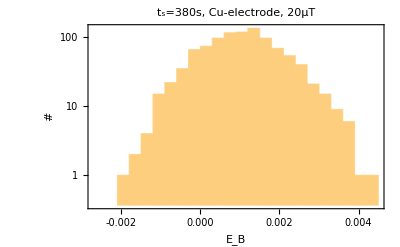

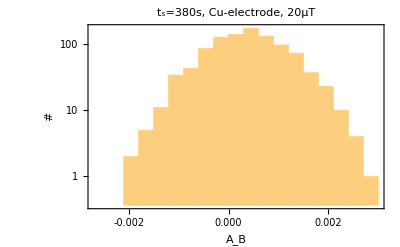

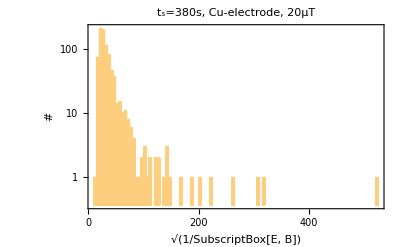

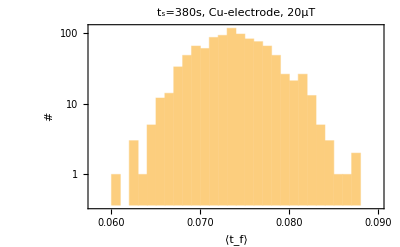

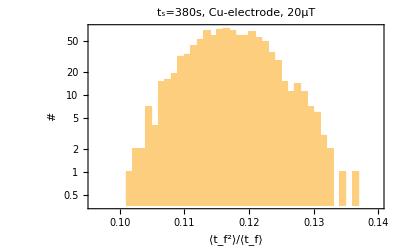

```mathematica
i=16;
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
maxsz=1000;
maxsz3=1000;
(*maxsz2=100000;*)
tf=Table[0,{k,1,maxsz}];
tf2tf=Table[0,{k,1,maxsz}];
If[i≤15,
kk=Position[tfal,descdat[[i]][[7]]+2*tsadd[[1]]][[1]][[1]];
tf=RandomVariate[NormalDistribution[tfal[[kk]][[2]],tfal[[kk]][[4]]],maxsz];
tf2tf=RandomVariate[NormalDistribution[tfal[[kk]][[5]],tfal[[kk]][[7]]],maxsz];
,
kk=Position[tfcu,descdat[[i]][[7]]+2*tsadd[[1]]][[1]][[1]];
tf=RandomVariate[NormalDistribution[tfcu[[kk]][[2]],tfcu[[kk]][[4]]],maxsz];
tf2tf=RandomVariate[NormalDistribution[tfcu[[kk]][[5]],tfcu[[kk]][[7]]],maxsz];
];
(***)
ab=RandomVariate[NormalDistribution[lvl3[[1]][[1]],lvl3[[1]][[2]]],maxsz3];
eb=RandomVariate[NormalDistribution[lvl3[[1]][[3]],lvl3[[1]][[4]]],maxsz3];
(*eb=RandomVariate[NormalDistribution[.0004,.00001],maxsz3];*)
tftseb0=Flatten[KroneckerProduct[1/eb,(descdat[[i]][[7]]+2tsadd[[1]])*tf2tf]];
tftsab=Flatten[KroneckerProduct[1/ab,(descdat[[i]][[7]]+2tsadd[[1]])/tf]];
tftseb=Flatten[KroneckerProduct[1/eb,(descdat[[i]][[7]]+2tsadd[[1]])/tf]];
Histogram[eb,{-.0027,.0045,.0003},PlotRange->Full,PlotRange->Full,Frame->True,FrameLabel->{"E_B","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[ab,{-.0027,.003,.0003},PlotRange->Full,PlotRange->Full,Frame->True,FrameLabel->{"A_B","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[Sqrt[1/eb],PlotRange->Full,Frame->True,FrameLabel->{"√(1/SubscriptBox[E, B])","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[tf,{.058,.09,.001},PlotRange->{{.058,.09},Automatic},Frame->True,FrameLabel->{"⟨t_f⟩","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[tf2tf,{.096,.14,.001},PlotRange->{Automatic,Automatic},Frame->True,FrameLabel->{"⟨t_f^2⟩/⟨t_f⟩","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
(*Histogram[Sqrt[tftseb0]]
Histogram[Sqrt[tftsab]]
Histogram[Sqrt[tftseb]]*)
```

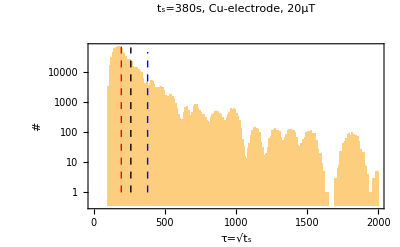

```mathematica
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{379,Log@(10^0)},{379,Log@(10^4.65)}}];
line2=Line[{{261,Log@(10^0)},{261,Log@(10^4.8)}}];
line3=Line[{{194,Log@(10^0)},{194,Log@(10^5.0)}}];
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l-N[Log10[2]],u+N[Log10[2]],int}]],3];
endpt=10000;
(*Histogram[{Sqrt[tftsab],Sqrt[tftseb]},{100,endpt,10},PlotRange->{{100,endpt},Automatic},ChartLegends->{"√(t_s/A_B)","√(t_s/((1 - SubscriptBox[E, B])·SubscriptBox[t, f]))"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],None},{LinTicks,None}},Frame->True,FrameLabel->{"τ/f(η)","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]*)
Show[{Histogram[Sqrt[tftseb0],{100,endpt/5,10},PlotRange->{{0,endpt/5},Automatic},Frame->True,FrameLabel->{"τ=√t_s","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT",
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{134,Log@(10^5.55)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{124,Log@(10^5.3)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{110,Log@(10^5.05)}],Large]}
}]}]
```

-829000.+4147.12 x-6.62496 x^2+0.00428914 x^3-3.93239×10^-8 x^4-1.87918×10^-9 x^5+1.4984×10^-12 x^6-6.59256×10^-16 x^7+1.93703×10^-19 x^8-4.04299×10^-23 x^9+6.12049×10^-27 x^10-6.67082×10^-31 x^11+4.97262×10^-35 x^12-2.05935×10^-39 x^13-2.32134×10^-44 x^14+1.01906×10^-47 x^15-7.75136×10^-52 x^16+3.36335×10^-56 x^17-9.02942×10^-61 x^18+1.40476×10^-65 x^19-9.75221×10^-71 x^20

InterpolatingFunction::dmval: Input value {100.202} lies outside the range of data in the interpolating function. Extrapolation will be used.

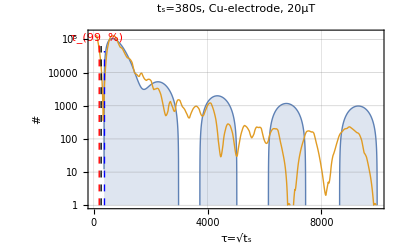

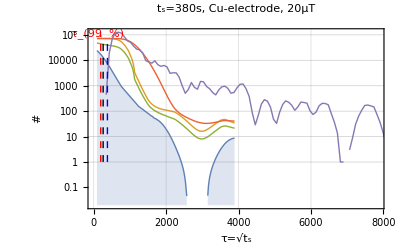

110

110

90

```mathematica
sigma=10;rr=10;
histlst=HistogramList[Sqrt[tftseb0]];
hstbl=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+4.2 histlst[[1]][[k]],histlst[[2]][[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
fthst=Fit[hstbl,Table[x^k,{k,0,20,1}],x]
fthst2=Interpolation[hstbl,InterpolationOrder->2];
estbckp=EstimatedBackground[hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm=-EstimatedBackground[-hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm2=-EstimatedBackground[-estbckm,10,Method->{"SNIP",10}];
ptbckp=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckp[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm2=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm2[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
Plot[{fthst,fthst2[x]},{x,100,10000},PlotRange->{{0,10000},{1,1.5*10^5}},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotStyle->Thick,Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT",
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{134,Log@(10^5.55)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{124,Log@(10^5.3)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{110,Log@(10^5.05)}],Large]}
}]
ListLinePlot[{ptbckp,ptbckm,(ptbckp+ptbckm)/2,ptbckm2,hstbl},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotStyle->Thick,Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT",
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{134,Log@(10^5.55)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{124,Log@(10^5.3)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{110,Log@(10^5.05)}],Large]}
}]
histhisttftseb0tot=Total[estbckm2];
cumhisttftseb0t=ParallelTable[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],Total[estbckm2[[;;k]]]/histhisttftseb0tot},{k,1,Dimensions[histlst][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val90]][[1]]]][[1]]
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val95]][[1]]]][[1]]
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val99]][[1]]]][[1]]
```

```mathematica
histhisttftseb0tot=Total[estbckm2];
cumhisttftseb0t=ParallelTable[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],Total[estbckm2[[;;k]]]/histhisttftseb0tot},{k,1,Dimensions[histlst][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val90]][[1]]]][[1]]
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val95]][[1]]]][[1]]
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val99]][[1]]]][[1]]
```

110

110

90

138.5

127.8

114.1

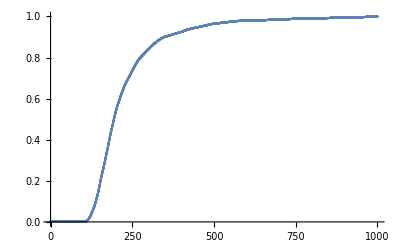

```mathematica
histtftseb0=HistogramList[Sqrt[tftseb0],{0,1000,.1}];
histtftseb0t=Transpose[{(histtftseb0[[1]][[;;-2]]+(histtftseb0[[1]][[2]]-histtftseb0[[1]][[2]])/2),histtftseb0[[2]][[;;]]}];
histhisttftseb0tot=Total[histtftseb0t[[;;,2]]];
cumhisttftseb0t=ParallelTable[{histtftseb0t[[k]][[1]],Total[histtftseb0t[[;;k,2]]]/histhisttftseb0tot},{k,1,Dimensions[histtftseb0t][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val90]][[1]]]][[1]]
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val95]][[1]]]][[1]]
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val99]][[1]]]][[1]]
ListPlot[cumhisttftseb0t,PlotRange->{{0,1000},{0,1}}]
```

```mathematica
val=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val]][[1]]]][[1]]
Sqrt[pttfmucu[[-1]][[2]][[1]]*pttfmucu[[-1]][[1]][[1]]/.00100883]
```

138.5

171.742

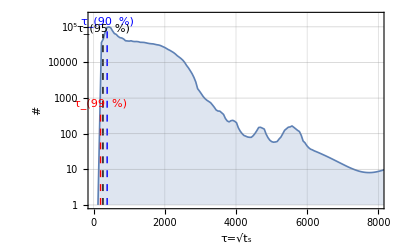

```mathematica
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{379,Log@(10^0)},{379,Log@(10^5.05)}}];
line2=Line[{{261,Log@(10^0)},{261,Log@(10^4.8)}}];
line3=Line[{{194,Log@(10^0)},{194,Log@(10^2.7)}}];
ListLinePlot[{Join[Table[{10k,.1},{k,0,10}],(ptbckm+hstbl)/2]},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotRange->{{1,7999},{1,2*10^5}},PlotStyle->Thickness[.003],Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{379,Log@(10^5.15)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{261,Log@(10^4.95)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{194,Log@(10^2.85)}],Large]}
}]
```

## Simply Playing!

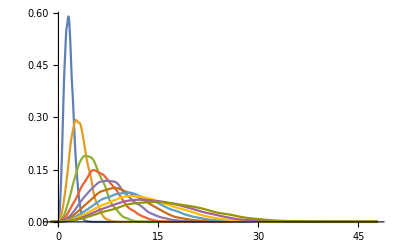

```mathematica
SmoothHistogram[Table[RandomVariate[MaxwellDistribution[k],10000],{k,1,10}],PlotRange->Full]
```

```mathematica
maxn=100000;
For[i=1,i≤ 10,i++,
randr=RandomVariate[MaxwellDistribution[1],maxn];
randt=RandomReal[{0,2Pi},2*maxn];
Print[Norm[Map[Mean,Table[{randr[[k]]Cos[randt[[k]]],randr[[k]]Sin[randt[[k]]]Cos[randt[[maxn+k]]],randr[[k]]Sin[randt[[k]]]Sin[randt[[maxn+k]]]},{k,1,maxn}]]]];
];//AbsoluteTiming
```

182.859

182.754

182.303

182.799

182.962

182.69

183.465

183.445

182.733

182.209

{18.223,Null}

```mathematica
Map[Norm,Table[{k,2k,3k},{k,1,10}]]
```

{√14,2 √14,3 √14,4 √14,5 √14,6 √14,7 √14,8 √14,9 √14,10 √14}

```mathematica
{46.331984274390216,Null}
```

{46.332,Null}

## A

97107.1-1.54656 x-0.00440453 x^2+7.09451×10^-7 x^3-5.30424×10^-11 x^4+2.38165×10^-15 x^5-7.11986×10^-20 x^6+1.49771×10^-24 x^7-2.28913×10^-29 x^8+2.58505×10^-34 x^9-2.16336×10^-39 x^10+1.32136×10^-44 x^11-5.58373×10^-50 x^12+1.34087×10^-55 x^13+5.67016×10^-62 x^14-1.96085×10^-66 x^15+8.64178×10^-72 x^16-2.14996×10^-77 x^17+3.30155×10^-83 x^18-2.93584×10^-89 x^19+1.16462×10^-95 x^20

InterpolatingFunction::dmval: Input value {100.202} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

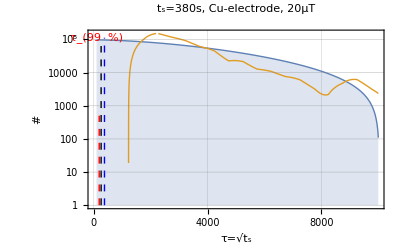

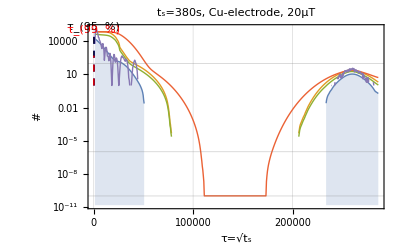

1750

1750

1250

```mathematica
sigma=10;rr=10;
histlst=HistogramList[Sqrt[tftsab]];
hstbl=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+ histlst[[1]][[k]],histlst[[2]][[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
fthst=Fit[hstbl,Table[x^k,{k,0,20,1}],x]
fthst2=Interpolation[hstbl,InterpolationOrder->2];
estbckp=EstimatedBackground[hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm=-EstimatedBackground[-hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm2=-EstimatedBackground[-estbckm,10,Method->{"SNIP",10}];
ptbckp=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckp[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm2=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm2[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
Plot[{fthst,fthst2[x]},{x,100,10000},PlotRange->{{0,10000},{1,1.5*10^5}},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotStyle->Thick,Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT",
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{134,Log@(10^5.55)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{124,Log@(10^5.3)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{110,Log@(10^5.05)}],Large]}
}]
ListLinePlot[{ptbckp,ptbckm,(ptbckp+ptbckm)/2,ptbckm2,hstbl},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotStyle->Thick,Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT",
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{134,Log@(10^5.55)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{124,Log@(10^5.3)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{110,Log@(10^5.05)}],Large]}
}]
histhisttftseb0tot=Total[estbckm2];
cumhisttftseb0t=ParallelTable[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],Total[estbckm2[[;;k]]]/histhisttftseb0tot},{k,1,Dimensions[histlst][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val90]][[1]]]][[1]]
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val95]][[1]]]][[1]]
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val99]][[1]]]][[1]]
```

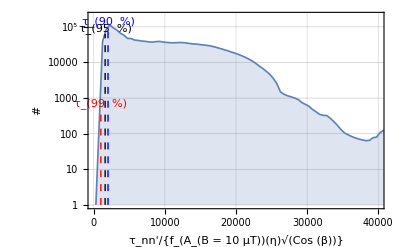

```mathematica
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{2014,Log@(10^0)},{2014,Log@(10^5.05)}}];
line2=Line[{{1610,Log@(10^0)},{1610,Log@(10^4.8)}}];
line3=Line[{{1007,Log@(10^0)},{1007,Log@(10^2.7)}}];
ListLinePlot[{Join[Table[{10k,.1},{k,0,10}],(ptbckm+hstbl)/2]},Frame->True,FrameLabel->{"τ_nn'/{f_(A_(B = 10  μT))(η)√(Cos (β))}","#"},PlotRange->{{1,39999},{1,2*10^5}},PlotStyle->Thickness[.003],Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{2014,Log@(10^5.15)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{1610,Log@(10^4.95)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{1007,Log@(10^2.85)}],Large]}
}]
```

## E

-514724.+760.15 x-0.12955 x^2-0.00022394 x^3+1.59717×10^-7 x^4-5.29979×10^-11 x^5+1.09501×10^-14 x^6-1.55214×10^-18 x^7+1.58069×10^-22 x^8-1.18276×10^-26 x^9+6.53618×10^-31 x^10-2.6272×10^-35 x^11+7.25403×10^-40 x^12-1.10311×10^-44 x^13-5.91619×10^-50 x^14+8.23593×10^-54 x^15-2.33708×10^-58 x^16+3.81907×10^-63 x^17-3.87474×10^-68 x^18+2.28262×10^-73 x^19-6.0084×10^-79 x^20

InterpolatingFunction::dmval: Input value {100.202} lies outside the range of data in the interpolating function. Extrapolation will be used.

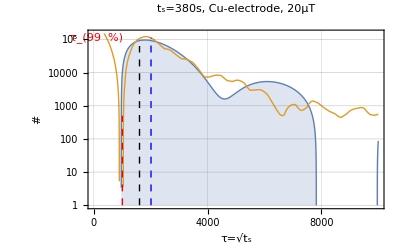

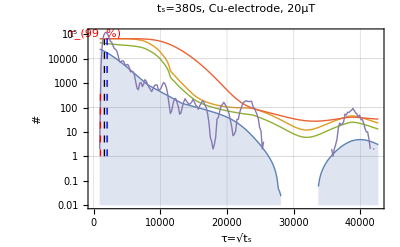

1100

1100

900

```mathematica
sigma=10;rr=10;
histlst=HistogramList[Sqrt[tftseb]];
hstbl=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+ histlst[[1]][[k]],histlst[[2]][[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
fthst=Fit[hstbl,Table[x^k,{k,0,20,1}],x]
fthst2=Interpolation[hstbl,InterpolationOrder->2];
estbckp=EstimatedBackground[hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm=-EstimatedBackground[-hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm2=-EstimatedBackground[-estbckm,10,Method->{"SNIP",10}];
ptbckp=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckp[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm2=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm2[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
Plot[{fthst,fthst2[x]},{x,100,10000},PlotRange->{{0,10000},{1,1.5*10^5}},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotStyle->Thick,Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT",
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{134,Log@(10^5.55)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{124,Log@(10^5.3)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{110,Log@(10^5.05)}],Large]}
}]
ListLinePlot[{ptbckp,ptbckm,(ptbckp+ptbckm)/2,ptbckm2,hstbl},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotStyle->Thick,Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT",
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{134,Log@(10^5.55)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{124,Log@(10^5.3)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{110,Log@(10^5.05)}],Large]}
}]
histhisttftseb0tot=Total[estbckm2];
cumhisttftseb0t=ParallelTable[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],Total[estbckm2[[;;k]]]/histhisttftseb0tot},{k,1,Dimensions[histlst][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val90]][[1]]]][[1]]
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val95]][[1]]]][[1]]
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val99]][[1]]]][[1]]
```

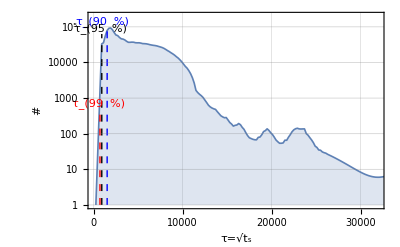

```mathematica
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{1514,Log@(10^0)},{1514,Log@(10^5.05)}}];
line2=Line[{{910,Log@(10^0)},{910,Log@(10^4.8)}}];
line3=Line[{{707,Log@(10^0)},{707,Log@(10^2.7)}}];
ListLinePlot[{Join[Table[{10k,.1},{k,0,10}],(ptbckm+hstbl)/2]},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotRange->{{1,31999},{1,2*10^5}},PlotStyle->Thickness[.003],Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{1014,Log@(10^5.15)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{710,Log@(10^4.95)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{507,Log@(10^2.85)}],Large]}
}]
```

## Sample Signal

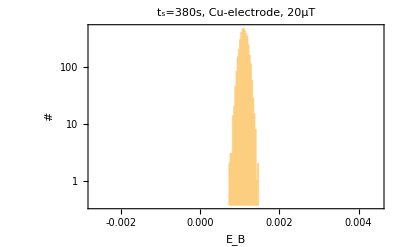

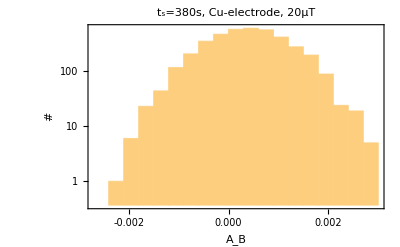

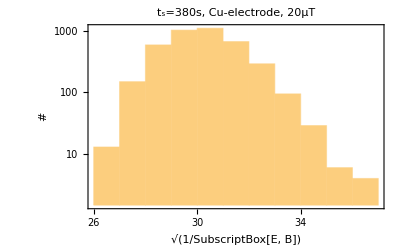

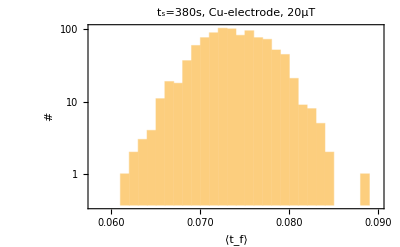

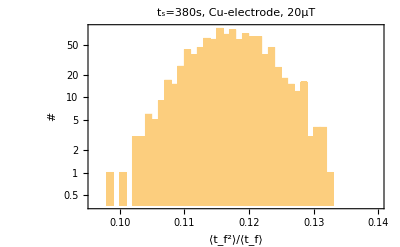

-1.08772×10^14+1.07953×10^12 x-4.41297×10^9 x^2+9.10766×10^6 x^3-8416.16 x^4-1.04339 x^5+0.00736247 x^6-2.97525×10^-7 x^7-6.11574×10^-9 x^8-6.19966×10^-13 x^9+4.97491×10^-15 x^10+1.94193×10^-18 x^11-3.61114×10^-21 x^12-2.8095×10^-24 x^13+2.34352×10^-27 x^14+3.00659×10^-30 x^15-1.86214×10^-33 x^16-2.62739×10^-36 x^17+3.23184×10^-39 x^18-1.31906×10^-42 x^19+1.95296×10^-46 x^20

InterpolatingFunction::dmval: Input value {100.202} lies outside the range of data in the interpolating function. Extrapolation will be used.

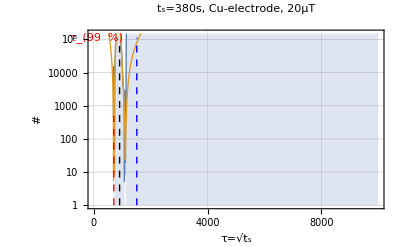

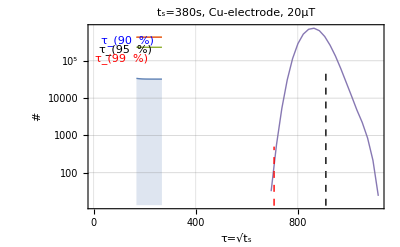

345/2

335/2

335/2

```mathematica
i=16;
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
maxsz=1000;
maxsz3=4000;
(*maxsz2=100000;*)
tf=Table[0,{k,1,maxsz}];
tf2tf=Table[0,{k,1,maxsz}];
If[i≤15,
kk=Position[tfal,descdat[[i]][[7]]+2*tsadd[[1]]][[1]][[1]];
tf=RandomVariate[NormalDistribution[tfal[[kk]][[2]],tfal[[kk]][[4]]],maxsz];
tf2tf=RandomVariate[NormalDistribution[tfal[[kk]][[5]],tfal[[kk]][[7]]],maxsz];
,
kk=Position[tfcu,descdat[[i]][[7]]+2*tsadd[[1]]][[1]][[1]];
tf=RandomVariate[NormalDistribution[tfcu[[kk]][[2]],tfcu[[kk]][[4]]],maxsz];
tf2tf=RandomVariate[NormalDistribution[tfcu[[kk]][[5]],tfcu[[kk]][[7]]],maxsz];
];
(***)
ab=RandomVariate[NormalDistribution[lvl3[[1]][[1]],lvl3[[1]][[2]]],maxsz3];
eb=RandomVariate[NormalDistribution[lvl3[[1]][[3]],lvl3[[1]][[4]]/10],maxsz3];
(*eb=RandomVariate[NormalDistribution[.0004,.00001],maxsz3];*)
tftseb0=Flatten[KroneckerProduct[1/eb,(descdat[[i]][[7]]+2tsadd[[1]])*tf2tf]];
tftsab=Flatten[KroneckerProduct[1/ab,(descdat[[i]][[7]]+2tsadd[[1]])/tf]];
tftseb=Flatten[KroneckerProduct[1/eb,(descdat[[i]][[7]]+2tsadd[[1]])/tf]];
Histogram[eb,{-.0027,.0045,.00003},PlotRange->Full,PlotRange->Full,Frame->True,FrameLabel->{"E_B","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[ab,{-.0027,.003,.0003},PlotRange->Full,PlotRange->Full,Frame->True,FrameLabel->{"A_B","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[Sqrt[1/eb],PlotRange->Full,Frame->True,FrameLabel->{"√(1/SubscriptBox[E, B])","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[tf,{.058,.09,.001},PlotRange->{{.058,.09},Automatic},Frame->True,FrameLabel->{"⟨t_f⟩","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[tf2tf,{.096,.14,.001},PlotRange->{Automatic,Automatic},Frame->True,FrameLabel->{"⟨t_f^2⟩/⟨t_f⟩","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
(*Histogram[Sqrt[tftseb0]]
Histogram[Sqrt[tftsab]]
Histogram[Sqrt[tftseb]]*)


(*****************************************)
sigma=10;rr=10;
histlst=HistogramList[Sqrt[tftseb0]];
hstbl=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+4.2 histlst[[1]][[k]],histlst[[2]][[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
fthst=Fit[hstbl,Table[x^k,{k,0,20,1}],x]
fthst2=Interpolation[hstbl,InterpolationOrder->2];
estbckp=EstimatedBackground[hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm=-EstimatedBackground[-hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm2=-EstimatedBackground[-estbckm,10,Method->{"SNIP",10}];
ptbckp=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckp[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm2=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm2[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
Plot[{fthst,fthst2[x]},{x,100,10000},PlotRange->{{0,10000},{1,1.5*10^5}},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotStyle->Thick,Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT",
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{134,Log@(10^5.55)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{124,Log@(10^5.3)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{110,Log@(10^5.05)}],Large]}
}]
ListLinePlot[{ptbckp,ptbckm,(ptbckp+ptbckm)/2,ptbckm2,hstbl},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotStyle->Thick,Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT",
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{134,Log@(10^5.55)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{124,Log@(10^5.3)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{110,Log@(10^5.05)}],Large]}
}]
histhisttftseb0tot=Total[estbckm2];
cumhisttftseb0t=ParallelTable[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],Total[estbckm2[[;;k]]]/histhisttftseb0tot},{k,1,Dimensions[histlst][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val90]][[1]]]][[1]]
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val95]][[1]]]][[1]]
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val99]][[1]]]][[1]]
```

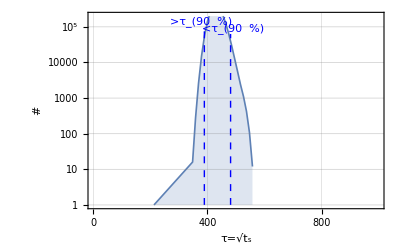

```mathematica
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{389,Log@(10^0)},{389,Log@(10^5.05)}}];
line2=Line[{{481,Log@(10^0)},{481,Log@(10^4.8)}}];
line3=Line[{{194,Log@(10^0)},{194,Log@(10^2.7)}}];
ListLinePlot[{Join[Table[{10k,.1},{k,0,10}],(hstbl)/2]},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotRange->{{1,999},{1,2*10^5}},PlotStyle->Thickness[.003],Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},
Epilog->{
{Directive[lineStyle1],line1,Style[Text[">τ_(90  %)",{379,Log@(10^5.15)}],Large]},
{Directive[lineStyle1],line2,Style[Text["<τ_(90  %)",{491,Log@(10^4.95)}],Large]}
}]
```